```mathematica
Clear["Global`*"]
```

# Weighted Integrals

## Cory Aitchison - February 2022

Trying to find the values of A, B that minimise the value of a weighted integral over the remainder to the DE

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
letters = {c, d, e, f, g, h, i, j, k};
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[letters[[n]][i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x];
```

```mathematica
<<"/Users/cory/Sync/USYD/Denison/Mathematica/PQSHelper.wl"
```

### Solutions

```mathematica
SubAnswers[eq_, n_] := SubAnswers[eq /. answer[n-1], n-1];
SubAnswers[eq_, 1] := eq;

GetEquation[n_]:= LDE[x |-> Sum[u[k][x], {k, 0, n}]] + NDE[x |-> Sum[u[k][x], {k, 0, n-1}]];
GetSolution[n_] := AnalyticSolve[SubAnswers[GetEquation[n], n], n, x, σ, letters[[n]]] // FullSimplify;

GetLinear[ans_] := Coefficient[(Last /@List @@@ ans)/. B->0 ,A, 1]A + Coefficient[(Last /@List @@@ ans)/. A->0 ,B, 1]B;
ShowLinear[n_]:=(x |-> PadRight[x, 2 + 2n,  _])/@GetLinear/@ (answer[#]&/@Range[1,n]) // Transpose// MatrixForm ;

ShowValues[n_] := (x |-> PadRight[x, 2 + 2n, _])/@((answer[#]/. param /. estimates)&/@Range[1,n])//Transpose//MatrixForm;

FinalFunction[n_] := SubAnswers[Sum[u[k][x], {k, 0, n}], n+1]/.param /. estimates;
FinalFunction[0] := u[0][x] /. param /. estimates;
```

```mathematica
f[x_]:= SubAnswers[u[1][x] + u[0][x], 2];
g[x_]:=SubAnswers[u[3][x] + u[2][x] + u[1][x] + u[0][x], 4];
h[x_] :=SubAnswers[u[5][x] + u[4][x] + u[3][x] + u[2][x] + u[1][x] + u[0][x], 6]
de[f_]:=x|->f''''[x] + 4 σ^4 f[x] + Γ f[x]^3;
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.445408, B -> 1.02817};
```

```mathematica
DumpGet["/Users/cory/Sync/USYD/Denison/Mathematica/answerSave.mx"]
```

## Weight function 1

We need a weight function (prior) that is 0 at x = 0 so that the numeric integration doesn’t break. And it must be such that the combined integral is finite, so the prior must be integrable.

```mathematica
w[x_]:=x^2Exp[-x^2]Cosh[2x]
```

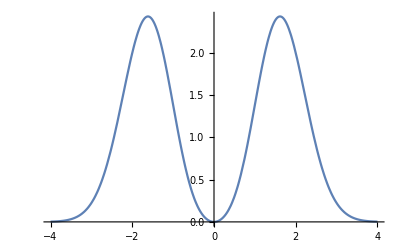

```mathematica
Plot[w[x], {x,-4,4}]
```

```mathematica
NIntegrate[w[x] (de[f][x])^2 /. param /. estimates, {x,-Infinity, Infinity}]
```

37.9818

```mathematica
NIntegrate[w[x] (de[f][x])^2 /. param /. {A->0.3, B->0.8}, {x,-Infinity, Infinity}]
```

54.9745

```mathematica
Plot3D[NIntegrate[w[x] (de[f][x])^2 /. param /. {A->a, B->b}, {x,-Infinity, Infinity}], {a, -1, 1}, {b,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[NIntegrate[w[x] (de[f][x])^2 /. param /. {A->a, B->b}, {x,-Infinity, Infinity}], {a, 0,2}, {b,0,2}]
```

-Graphics3D-

### Find minimum

```mathematica
criterion[a_,b_] :=NIntegrate[w[x] (de[f][x])^2 /. param /. {A->a, B->b}, {x,-Infinity, Infinity}];
```

```mathematica
vals = Table[criterion[a,b],{a,0.1, 2, 0.1},{b, 0.1, 2, 0.1}];
```

```mathematica
Min[vals]
```

1.93857

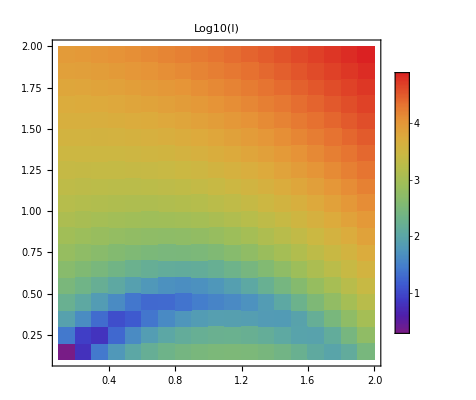

```mathematica
ListDensityPlot[Log10[vals], Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.1, 2}, {0.1, 2}}, ColorFunction->"Rainbow", PlotLabel->"Log10(I)"]
```

Let’s scale these values by the amplitude^2:

```mathematica
valsscaled = vals / Table[(a+b)^2, {a, 0.1, 2, 0.1}, {b, 0.1, 2, 0.1}];
```

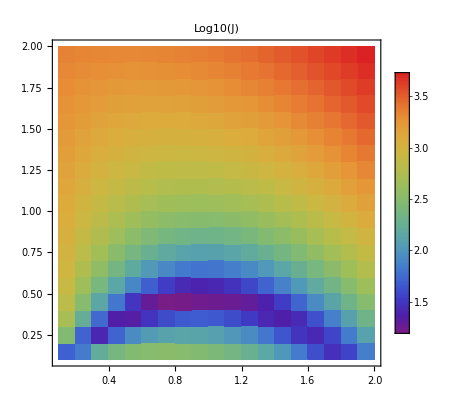

```mathematica
ListDensityPlot[Log10[valsscaled], Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.1, 2}, {0.1, 2}}, ColorFunction->"Rainbow", PlotLabel->"Log10(J)"]
```

### Zoom in on the region

```mathematica
vals2 = Table[criterion[a,b] / (a+b)^2,{a,0.3, 0.5, 0.01},{b, 0.7, 1.2, 0.01}];
```

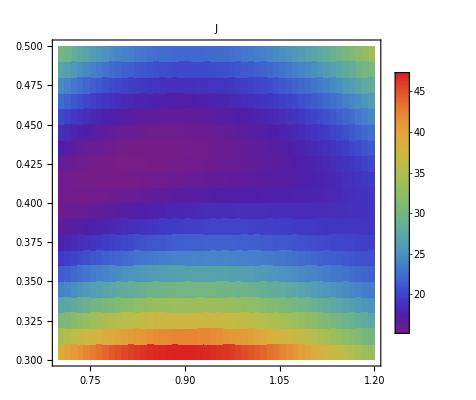

```mathematica
ListDensityPlot[vals2, Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.7, 1.2}, {0.3, 0.5}}, ColorFunction->"Rainbow", PlotLabel->"J"]
```

```mathematica
estimates
```

{A→0.445408,B→1.02817}

## New prior

```mathematica
criterion[a_,b_, w_] :=NIntegrate[w[x] (de[f][x] / (A  + B))^2 /. param /. {A->a, B->b}, {x,-Infinity, Infinity}];
```

```mathematica
w2[x_]:= If[Abs[x] < 0.1, 0, Exp[-x^2]]
```

```mathematica
w3[x_]:=Exp[-x^2] - Exp[-10x^2];
```

```mathematica
criterion[A /. estimates, B /. estimates, w3]
```

48.0104

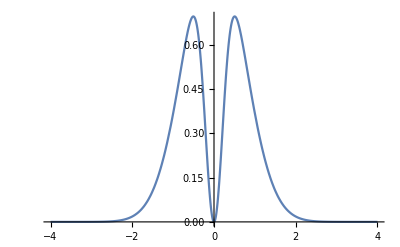

```mathematica
Plot[w3[x], {x,-4,4}]
```

```mathematica
vals3 = Table[criterion[a,b, w3] / (a+b)^2,{a,0.3, 0.5, 0.01},{b, 0.7, 1.2, 0.01}];
```

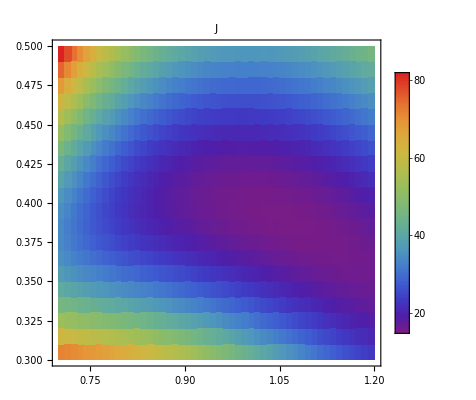

```mathematica
ListDensityPlot[vals3 , Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.7, 1.2}, {0.3, 0.5}}, ColorFunction->"Rainbow", PlotLabel->"J"]
```

## Flat weight function

```mathematica
wflat[x_]:= If[Abs[x] <= 0.01 , 0, 1/4];
criterion[a_,b_, w_] :=NIntegrate[w[x] (de[f][x] / (A  + B))^2 /. param /. {A->a, B->b}, {x,-2, 2}];
```

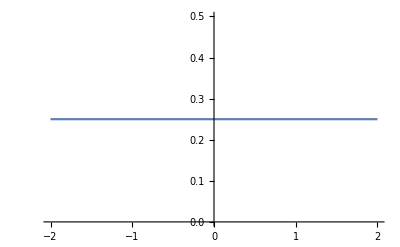

```mathematica
Plot[wflat[x], {x,-2,2}]
```

```mathematica
criterion[A /. estimates, B /. estimates, wflat]
```

39.7271

```mathematica
valsflat = Table[criterion[a,b, wflat] / (a+b)^2,{a,0.3, 0.5, 0.01},{b, 0.7, 1.2, 0.01}];
```

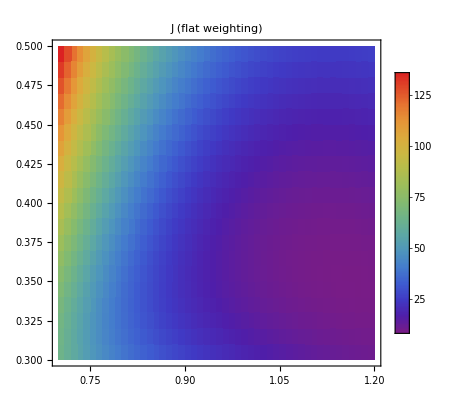

```mathematica
ListDensityPlot[valsflat , Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.7, 1.2}, {0.3, 0.5}}, ColorFunction->"Rainbow", PlotLabel->"J (flat weighting)"]
```

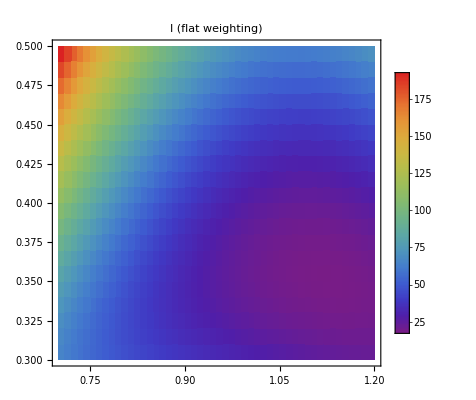

```mathematica
ListDensityPlot[valsflat * Table[(a+b)^2, {a, 0.3, 0.5, 0.01}, {b,0.7, 1.2, 0.01}] , Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.7, 1.2}, {0.3, 0.5}}, ColorFunction->"Rainbow", PlotLabel->"I (flat weighting)"]
```

```mathematica
valsflat2 = Table[criterion[a,b, wflat] / (a+b)^2,{a,0.1, 1.5, 0.05},{b, 0.1, 1.5, 0.05}];
```

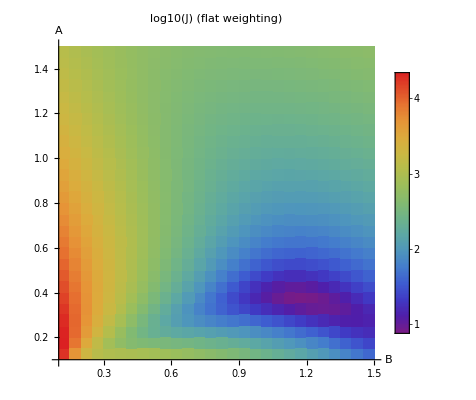

```mathematica
ListDensityPlot[valsflat2 // Log10 , Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.1, 1.5}, {0.1, 1.5}}, ColorFunction->"Rainbow", PlotLabel->"log10(J) (flat weighting)", Axes -> True, AxesLabel->{B,A}, Frame->False, AxesOrigin->{0.1,0.1}]
```

## Higher order

Consider u0 + u1 + u2 + u3

```mathematica
wflat[x_]:= If[Abs[x] <= 0.01 , 0, 1/4];
criterion[a_,b_,func_, w_] :=NIntegrate[w[x] (de[func][x] / (A  + B))^2 /. param /. {A->a, B->b}, {x,-2, 2}];
```

```mathematica
criterion[0.5, 0.5, g, wflat]
```

1263.11

```mathematica
valsflatu3 = Table[criterion[a,b, g, wflat] / (a+b)^2,{a,0.1, 1.5, 0.05},{b, 0.1, 1.5, 0.05}];
```

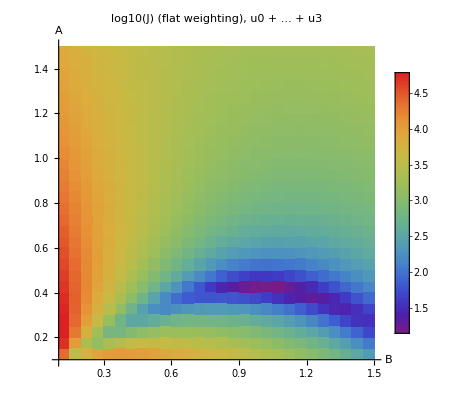

```mathematica
ListDensityPlot[Log10[valsflatu3 ], Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.1, 1.5}, {0.1, 1.5}}, ColorFunction->"Rainbow", PlotLabel->"log10(J) (flat weighting), u0 + ... + u3", Axes -> True, AxesLabel->{B,A}, Frame->False, AxesOrigin->{0.1,0.1}]
```

```mathematica
valsflatu3zoom = Table[criterion[a,b, g, wflat] / (a+b)^2,{a, 0.35, 0.5, 0.005},{b,0.85, 1.15, 0.01}];
```

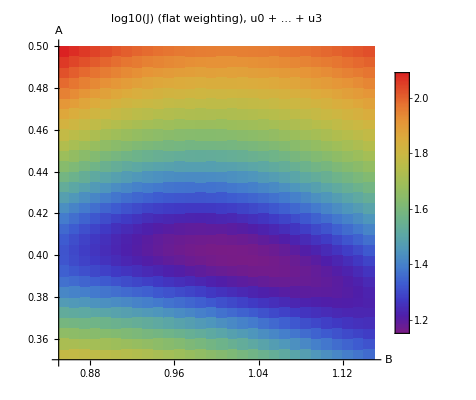

```mathematica
ListDensityPlot[Log10[valsflatu3zoom ], Mesh -> None, InterpolationOrder->0, PlotLegends->Automatic, DataRange->{{0.85, 1.15},{0.35, 0.5}}, ColorFunction->"Rainbow", PlotLabel->"log10(J) (flat weighting), u0 + ... + u3", Axes -> True, AxesLabel->{B,A}, Frame->False, AxesOrigin->{0.85,0.35}]
```

## Save values

```mathematica
DumpSave["/Users/cory/Sync/USYD/Denison/Mathematica/05_weighted_220201.mx", {valsflat, valsflat2, valsflatu3, valsflatu3zoom}];
```